```mathematica
dataset=ExampleData[{"MachineLearning","Titanic"},"Data"];
```

```mathematica
Dimensions[dataset]
```

{1309}

```mathematica
train=dataset[[;;1000]];
test=dataset[[1001;;]];
```

```mathematica
testSurvived=If[#=="survived",1,0]&/@test[[;;,2]];
trainSurvived=If[#=="survived",1,0]&/@train[[;;,2]];
trainData=train[[;;,1]];
testData=test[[;;,1]];
```

```mathematica
c=Classify[train,Method->"LogisticRegression"]
```

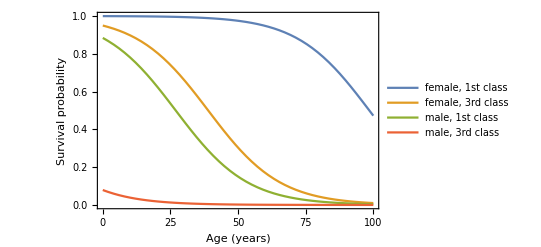

```mathematica
p[class_,age_,sex_]:=c[{class,age,sex},{"Probability","survived"}];
Plot[{p["1st",x,"female"],p["3rd",x,"female"],p["1st",x,"male"],p["3rd",x,"male"]},{x,0,100},PlotLegends->{"female, 1st class","female, 3rd class","male, 1st class","male, 3rd class"},Frame->True,FrameLabel->{"Age (years)","Survival probability"}]
```

```mathematica
pTest[x_]:=c[x,{"Probability","survived"}];
```

```mathematica
predictionTrain=If[#>.5,1,0]&/@(pTest[#]&/@ trainData );
```

```mathematica
check=Table[If[trainSurvived[[i]]==predictionTrain[[i]],1,0],{i,1000}];
```

```mathematica
Plus@@check/1000.
```

0.791

```mathematica
235/309.
```

0.760518

```mathematica
check//Length
```

1000

```mathematica
Do[
predictionTrain=If[#>i/10.,1,0]&/@(pTest[#]&/@ trainData );
check=Table[If[trainSurvived[[i]]==predictionTrain[[i]],1,0],{i,1000}];
Print[i/10.,Plus@@check/1000.],
{i,0,10}]
```

0.0.423

0.10.738

0.20.773

0.30.779

0.40.772

0.50.791

0.60.793

0.70.801

0.80.794

0.90.78

1.0.577

```mathematica
Do[
predictionTest=If[#>i/10.,1,0]&/@(pTest[#]&/@ testData );
check=Table[If[testSurvived[[i]]==predictionTest[[i]],1,0],{i,309}];
Print[i/10.,Plus@@check/309.],
{i,0,10}]
```

0.0.249191

0.10.760518

0.20.757282

0.30.757282

0.40.760518

0.50.770227

0.60.770227

0.70.760518

0.80.747573

0.90.7411

1.0.750809